charge density at mu_n=1200, mu_e = 100.0:   5.6129e6 MeV^3

charge density in protons and electrons: 5.6129e6 MeV^3

charge density discrepancy: -9.3132e-10 MeV^3

charge density == protons - electrons  OK

-m$p+√(m$e^2+2 mu$n m$p-m$p^2)

neutral beta-equil nucleon density at mu_n=1200:  1.198911e7 MeV^3

neutral beta-equil pressure deriv  at mu_n=1200:  1.198911e7 MeV^3

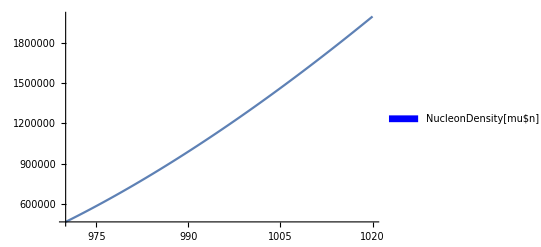

997.808

neutral beta-equil nuclear matter: mu_n = 997.808 MeV

neutral beta-equil nuclear matter: mu_e = 57.7583 MeV

Estimated radius of Lead nucleus is 0.0342558 MeV^-1  =  6.75959 fm

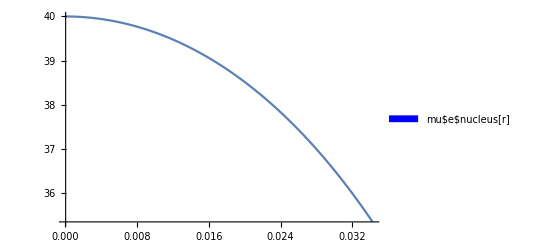

Z alpha / R for Lead = 17.4727 MeV

For Lead with mu_e(0) = 39 MeV,  mu_e(R)= 33.9557 MeV

For Lead with mu_e(0) = 25 MeV,  mu_e(R)= 32.4293 MeV

For Lead, mu_e(r=0) = 27.5837 MeV

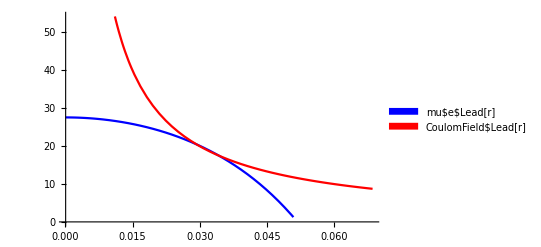

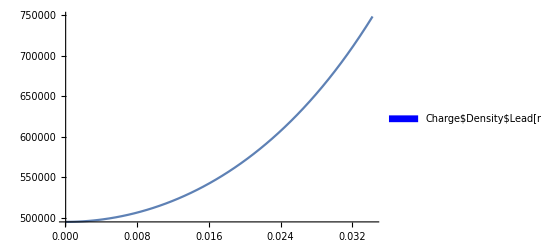

Where is the positive charge concentrated: Previous plot shows as we approach to the surface of nuleus, charge density incresese,
 which means that charge is concentrated mainly on the surface of nucleus.

Charge on Lead nucleus in TF calculation is 107.565  expected 82

Explian: One of the effective elements on behavior of collective particles is Coulomb's force,
 which we have ignored it in our model. Since coulmb's force can repel the particles with the same charge,
 it will reduce the charge density and consequently atomic number of Lead.

```mathematica
(*Physics 584,Computational Methods,Mark Alford,Jan 2015 Exercise 2:Modeling a nucleus as a gas of free nucleons*)(*Set up relativistic and nonrelativistic free Fermi gas*)
e$1[p_,m_]=Module[{},Sqrt[p^2+m^2]];
number$density[pF_,m_]=Module[{},pF^3/(3*Pi^2)];
energy$density[pF_,m_]=Module[{p},1/Pi^2*Integrate[e$1[p,m]*p^2,{p,0,pF},Assumptions->{pF>0,m>0}]];
pFermi[mu_,m_]=Module[{},Sqrt[mu^2-m^2]];
pressure[mu_,m_]=Module[{pF},pF=pFermi[mu,m];
Simplify[mu*number$density[pF,m]-energy$density[pF,m],{mu>m,m>0}]];

e$NR[p_,m_]=Module[{},m+p^2/(2*m)];
pFermi$NR[mu_,m_]=Module[{},Sqrt[2*m*(mu-m)]];
number$density$NR[pF_,m_]=Module[{},pF^3/(3*Pi^2)];
(*as before*)
energy$density$NR[pF_,m_]=Module[{p},1/Pi^2*Integrate[e$NR[p,m]*p^2,{p,0,pF},Assumptions->{pF>0}]];
pressure$NR[mu_,m_]=Module[{pF},pF=pFermi$NR[mu,m];
Simplify[mu*number$density$NR[pF,m]-energy$density$NR[pF,m],{mu>m,m>0}]];


(*Some physical constants:*)

MeV$fm=197.326960;(*For converting MeV to fm^-1 and vice versa*)(*so 1fm=1/200=0.005 MeV^-1*)Mneutron=939.565378;(*All quantities will be in MeV*)Mproton=938.272013;
Melectron=0.51100;
mass$rules={m$p->Mproton,m$n->Mneutron,m$e->Melectron};
(*In our functions we will write the masses of the particles as m$p,m$n,m$e,and when we want to obtain numbers we will apply mass$rules*)

alpha=1/137.0;(*fine structure constant:coupling strength of electromagnetism*)(*We model nuclear matter as a gas of noninteracting neutrons,protons,and electrons.Create a function that calculates the pressure of such a gas as a function of separate chemical potentials for these particles:*)pressure$NM[mu$p_,mu$n_,mu$e_]=Module[{},pressure$NR[mu$p,m$p]+pressure$NR[mu$n,mm$n]+pressure[mu$e,m$e](*assume m$p,m$n,m$e are global variables,and that neutrons and protons are nonrelativistic,but electrons are relativistic*)];

(*In "beta-equilibrated" nuclear matter,the weak interactions have allowed neutrons to convert to protons and vice versa,so mu$n=mu$p+mu$e in beta-equilibrium.Create functions that give the pressure,charge density,and nucleon density of beta-equilibrated nuclear matter.*)

pressure$NM$beta[mu$n_,mu$e_]=Module[{},pressure$NR[mu$n-mu$e,m$p]+pressure$NR[mu$n,m$n]+pressure[mu$e,m$e]];
charge$density$NM$beta[mu$n_,mu$e_]=Module[{},FullSimplify[-D[pressure$NM$beta[mu$n,mu$e],mu$e]](*use a suitable derivative of the appropriate pressure function Note that elec charge is
-d p/d mu$e because mu$e is the chemical potential for negative charge*)];

nucleon$density$NM$beta[mu$n_,mu$e_]=Module[{},FullSimplify[D[pressure$NM$beta[mu$n,mu$e],mu$n]](*use a suitable derivative of the appropriate pressure function*)];
charge$density$NM[mu$p_,mu$n_,mu$e_]=Module[{},FullSimplify[D[pressure$NM[mu$p,mu$n,mu$e],mu$p]-D[pressure$NM[mu$p,mu$n,mu$e],mu$e]]];
(*make an alternate definition of charge density:proton density minus electron density*)
charge$density$NM$alt[mu$n_,mu$e_]=Module[{mu$p=mu$n-mu$e},charge$density$NM[mu$p,mu$n,mu$e](*to be filled in*)];

(*Run the following code,which checks that the two charge density functions agree by plugging in numbers for mu$n and mu$e and applying mass$rules:*)

Print["charge density at mu_n=1200, mu_e = 100.0:   ",CForm[SetPrecision[charge$density$NM$beta[1200.0,100.0]/.mass$rules,5]]," MeV^3"];
Print["charge density in protons and electrons: ",CForm[SetPrecision[charge$density$NM$alt[1200.0,100.0]/.mass$rules,5]]," MeV^3"];
Print["charge density discrepancy: ",CForm[SetPrecision[(charge$density$NM$beta[1200.0,100.0]-charge$density$NM$alt[1200.0,100.0])/.mass$rules,5]]," MeV^3"];

(*Check that the difference between the two functions simplifies algebraically to zero*)
If[(*fill in here*)FullSimplify[charge$density$NM$alt[mu$n,mu$e]-charge$density$NM$alt[mu$n,mu$e]]==0
,Print["charge density == protons - electrons  OK"],(*else*)Print["**** charge density == protons - electrons failed!"]];



(*EXTRA CREDIT:charge$density$NM$alt is a simpler expression than charge$density$NM$beta.Can you get Mathematica to simplify charge$density$NM$beta so that it looks the same as charge$density$NM$alt?I couldn't manage it.*)


(*Now impose electrical neutrality:the electric charge density should be zero in large volumes of beta-equilibrated nuclear matter.This requirement determines mu$e as a function of mu$n:*)

mu$e$neutral[mu$n_]=Module[{},soln=Solve[charge$density$NM$alt[mu$n,mu$e]==0,mu$e(*calculate what value of the electron chem pot gives zero charge density*)]];
mu$e$neutral[mu$n_]=mu$e/.soln[[2]]

(*Use this to write the pressure and nucleon density of neutral beta-equilibrated nuclear matter as a function of mu$n only:*)

pressure$NM$beta$neutral[mu$n_]=Module[{mu$e=mu$e$neutral[mu$n]},FullSimplify[pressure$NM$beta[mu$n,mu$e]]];(*to be filled in*)
nucleon$density$NM$beta$neutral[mu$n_]=Module[{mu$e=mu$e$neutral[mu$n]},FullSimplify[nucleon$density$NM$beta[mu$n,mu$e]]];(*to be filled in*)(*This code checks that for neutral,beta-equilibrated nuclear matter,the nucleon density agrees with the appropriate derivative of the pressure,by plugging in numbers:*)Print["neutral beta-equil nucleon density at mu_n=1200:  ",CForm[SetPrecision[nucleon$density$NM$beta$neutral[1200.0]/.mass$rules,8]]," MeV^3"];
Print["neutral beta-equil pressure deriv  at mu_n=1200:  ",CForm[SetPrecision[D[pressure$NM$beta$neutral[mu$n],mu$n]/.{mu$n->1200.0}/.mass$rules,8]]," MeV^3"];

(*EXTRA CREDIT:Can you show that the two expressions are algebraically identical?I couldn't manage it using Simplify:If[FullSimplify[nucleon$density$NM$beta$neutral[mu$n]-D[pressure$NM$beta$neutral[mu$n],mu$n],{m$n>m$p+m$e,m$p>0,m$e>0,mu$n>m$n}]==0,Print["neutral beta-equil nucleon density == deriv of pressure OK"],Print["**** neutral beta-equil nucleon density == deriv of pressure failed!"]];*)

(*Now we start putting in numbers to apply this simple model to real-world nuclei.The nucleon density of nuclei is 0.16 nucleons per fm^3. But we will express everything in MeV,so we need to convert that to MeV^3:*)

nucleon$density$expt=0.16*MeV$fm^3;

(*Plot the nucleon density of neutral beta-equilibrated nuclear matter,converted to fm^-3,as a function of mu$n,over a reasonable range of values of mu$n,to see roughly where it has the physical value of 0.16 nucleons/fm^3*)
legend1=Grid[{{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->5],"NucleonDensity[mu$n]"}}];
Plot[nucleon$density$NM$beta$neutral[mu]/.mass$rules,{mu,970,1020},PlotLegends->legend1]
(*Use FindRoot to obtain the value of mu$n at which our free nucleon gas has the density of real nuclear matter.Use mass$rules to give the particles their physical mass values.*)
nucleon$density$NM$beta$neutral$soln[mu$n0_]=nucleon$density$NM$beta$neutral[mu$n0]/.mass$rules ;
mu$n$NM=mu$n0/.FindRoot[nucleon$density$NM$beta$neutral$soln[mu$n0] == nucleon$density$expt,{mu$n0,970}](*to be filled in.Note that this is a calculation of a number,not a function definition.*)
Print["neutral beta-equil nuclear matter: mu_n = ",mu$n$NM," MeV"];

(*Print out the value of mu$e in neutral beta-equilibrated nuclear matter at nuclear density*)

Print["neutral beta-equil nuclear matter: mu_e = ",mu$e$neutral[mu$n$NM]/.mass$rules(*to be filled in*)," MeV"];


(*Write a function that estimates the radius (in MeV^-1) of a nucleus of atomic mass number (total number of nucleons) A,assuming that the nucleus is a sphere with nucleon density nucleon$density$expt.*)

nuclear$radius[A_]=Module[{},(3A/(4π*nucleon$density$expt))^(1/3)(*to be filled in*)];


(*Now we estimate the expected radius of a Lead nucleus Z=82,A=207,in MeV and fm*)

Z$Lead=82;
A$Lead=207;
R$Lead=nuclear$radius[A$Lead];
R$Lead$fm=R$Lead*MeV$fm;

Print["Estimated radius of Lead nucleus is ",R$Lead," MeV^-1  =  ",R$Lead$fm," fm"];


(*Finally,we will try to estimate the charge distribution of a nucleus of charge Z and radius R.We treat the nucleus as a sphere of nuclear matter in which mu$e is different from its neutrality value,but mu$n stays at mu$n$NM.We use the Thomas-Fermi method:solve the self-consistent Poisson equation to get mu$e$nucleus[Z,R,r] and charge$density$nucleus[Z,R,r] with boundary conditions mu$e'[0]==0 (no charge at center) mu$e[R]==Z*alpha/R (match to Coulomb potl in vacuum,ignoring electron cloud outside nucleus for now) Shooting method:choose mu$e[0] and evolve to R,varying mue[0] until it obeys the BC at R.*)

r$center=0.01/MeV$fm;(*diffeq has 1/r^2 in it,so start at r just above 0*)Evolve$mu$e[Z_?NumericQ,R_?NumericQ,mue$center_?NumericQ]:=Module[{},NDSolve[{(mu$e$nucleus''[r]+(2/r)mu$e$nucleus'[r]+4*Pi *alpha * charge$density$NM$alt[mu$n$NM,mu$e$nucleus[r]]/.mass$rules)==0,mu$e$nucleus[r$center]==mue$center,mu$e$nucleus'[r$center]==0},mu$e$nucleus[r],{r,r$center,R}](*solve the diffeq for mu$e[r$center]==mue$center,and return the result as an InterpolatingFunction*)];
(*Write a function to calculate and plot mu$e[r] for a nucleus of given charge Z and radius R,with a given guess for mue$center*)
legend2=Grid[{{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->5],"mu$e$nucleus[r]"}}];
make$mue$plot[Z_?NumericQ,R_?NumericQ,mue$center_?NumericQ]:=Module[{},mue=Evolve$mu$e[Z,R,mue$center];(*to be filled in*)Show[Plot[Evaluate[Evolve$mu$e[Z,R,mue$center]/.mue](*to be filled in*),{r,r$center,R},PlotLegends->legend2]]];
(*Call this function to make a plot of mu$e(r) for a Lead nucleus with mu$e=40MeV at the center.Note how mu$e varies with r.*)

make$mue$plot[Z$Lead,R$Lead,40.0]

(*We need to choose mu$e(r$center) so that at r=R mu$e agrees with the external Coulonb field of a nucleus of charge Z,which varies with radius as Z*alpha/r.To do this,first create a function that uses Evolve$mu$e to calculate mu$e at the edge of a nucleus of given charge,radius,and central mu$e:*)

mu$e$at$R[Z_?NumericQ,R_?NumericQ,mue$center_?NumericQ]:=Module[{},NDSolveValue[{(mu$e$nucleus''[r]+(2/r)mu$e$nucleus'[r]+4*Pi *alpha * charge$density$NM$alt[mu$n$NM,mu$e$nucleus[r]]/.mass$rules)==0,mu$e$nucleus[r$center]==mue$center,mu$e$nucleus'[r$center]==0},mu$e$nucleus[R],{r,r$center,R}](*to be filled in*)];

(*Try it out for a Lead nucleus.First evaluate the external Coulomb field Z*alpha/R at the edge of a Lead nucleus,then evaluate mu$e$at$R[...] for a Lead nucleus with different values of mu$e$center,and see roughly what value of mu$e$center will lead to agreement.*)

Print["Z alpha / R for Lead = ",(Z$Lead*alpha)/R$Lead(*to be filled in*)," MeV"];

Print["For Lead with mu_e(0) = ",39(*fill in a value of mu$e$center*)," MeV,","  mu_e(R)= ",mu$e$at$R[Z$Lead,R$Lead,39](*fill in*)," MeV"];
Print["For Lead with mu_e(0) = ",25(*fill in a value of mu$e$center*)," MeV,","  mu_e(R)= ",mu$e$at$R[Z$Lead,R$Lead,37.90412](*fill in*)," MeV"];


(*Write a function that solves for the correct value of mu$e at r=0 in a nucleus of any Z and R.Use FindRoot,and use the results of your numerical calculation for Lead to choose a reasonable starting range for mu$e at r=0.*)


mu$e$center[Z_?NumericQ,R_?NumericQ]:=Module[{},(*to be filled in*)mu$e$at$R$alt/.FindRoot [mu$e$at$R[Z,R,mu$e$at$R$alt]-Z$Lead*alpha/R$Lead,{mu$e$at$R$alt,25}]];

(*Use the mu$e$center function to find out what mu$e is in the center of a Lead nucleus:*)

Print["For Lead, mu_e(r=0) = ",mu$e$center[Z$Lead,R$Lead]," MeV"];

(*Create a function that calculates mu$e[r] inside a nucleus of charge Z and radius R.It will use Evolve$mu$e to create the InterpolatingFunction,and it will use mu$e$center to choose the central value of mu$e as an initial condition for Evolve$mu$e,It will return mu$e[r] as an InterpolatingFunction*)

mu$e$of$r[Z_?NumericQ,R_?NumericQ]:=Module[{},NDSolveValue[{(mu$e''[r]+(2/r)mu$e'[r]+4*Pi *alpha * charge$density$NM$alt[mu$n$NM,mu$e[r]]/.mass$rules)==0,mu$e[r$center]==mu$e$center[Z,R],mu$e'[r$center]==0},mu$e,{r,r$center,2*R}](*to be filled in*)];

(*Use this to create an interpolating function that gives mu$e(r) for Lead*)

mu$e$of$r$Lead=mu$e$of$r[Z$Lead,R$Lead];

(*Plot this function and the external Coulomb field on the same axes.The horizontal axis should go from r$center to 2*R$Lead.*)
mu$e$r=NDSolveValue[{(mu$e''[r]+(2/r)mu$e'[r]+4*Pi *alpha * charge$density$NM$alt[mu$n$NM,mu$e[r]]/.mass$rules)==0,mu$e[r$center]==mu$e$center[Z$Lead,R$Lead],mu$e'[r$center]==0},mu$e,{r,r$center,2*R$Lead}];
legend3=Grid[{{Graphics[{{Blue,Disk[{0,0},0.1]}},ImageSize->5],"mu$e$Lead[r]"},{Graphics[{{Red,Disk[{0,1},0.1]}},ImageSize->5],"CoulomField$Lead[r]"}}];
Plot[{mu$e$r[r],alpha Z$Lead/r},{r,r$center,2*R$Lead},PlotStyle->{Blue,Red},PlotLegends->legend3]
(*Create a function that gives the charge density of the Lead nucleus,as a function of radius from the center.*)

charge$density$Lead[r_]=Module[{},(charge$density$NM$alt[mu$n$NM,mu$e$r[r]]/.mass$rules)(*fill in*)];

(*Make a plot of the charge density of the Lead nucleus,as a function of radius from the center.Where is the positive charge concentrated?*)

legend4=Grid[{{Graphics[{{Blue,Disk[{0,0},0.1]}},ImageSize->5],"Charge$Density$Lead[r]"}}];
Plot[charge$density$Lead[r],{r,r$center,R$Lead},PlotLegends->legend4]

Print["Where is the positive charge concentrated: Previous plot shows as we approach to the surface of nuleus, charge density incresese,\n which means that charge is concentrated mainly on the surface of nucleus."]
(*Calculate the total charge of the nucleus by integrating the charge density function over the nucleus:*)

Z$Lead$TF=Module[{r},N[4π Integrate[charge$density$Lead[r]*r^2,{r,r$center,R$Lead}]]];

Print["Charge on Lead nucleus in TF calculation is ",Z$Lead$TF,"  expected ",Z$Lead];
(*One would expect the result to be Z$Lead,but it disagrees slightly.Can you explain why?*)
Print["Explian: One of the effective elements on behavior of collective particles is Coulomb's force,\n which we have ignored it in our model. Since coulmb's force can repel the particles with the same charge,\n it will reduce the charge density and consequently atomic number of Lead."]



(*----------------------------------------------------------------------To save a notebook as a.m file,1) Preparation:For every cell that you want to save to the.m file,move the cursor to the right hand edge of the cell (in the "square bracket" region where the cursor becomes an arrow pointing to the left),right click,and then click on the "Initialization Cell" button.Just do this for definitions and evaluations of expressions.Don't save graphics cells,since they will be regenerated when the.m file is imported into mathematica.2) Saving:File->Save As under "Files of Type:" select Mathematica Package (.m) give the file a name and save it 3) Checking:Quit mathematica and restart it.File->Open->select the.m file you just created and open it Go through the initialization cells evaluating them and making sure that they work OK.----------------------------------------------------------------------*)
```